## Asynchronous Updating

An important feature of cellular automata is the assumption that all cell values are updated “simultaneously” or “synchronously” in a definite series of steps. But in practical examples of distributed consensus one’s often dealing with values that are instead updated asynchronously. In effect, what one wants is to “break down” the synchronous updating of an ordinary cellular automaton into a sequence of updates of individual cells, with the order of these updates not being specified by any particular rule.
So an obvious first question is: “Does it actually matter in what order these individual updates are done?” And sometimes it doesn’t. Here's an example. Instead of an ordinary cellular automaton, consider a block cellular automaton in which at each step pairs of values adjacent cells are replaced by new values:

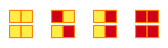

```mathematica
RulePlot[SubstitutionSystem[{{0, 0}-> {0, 0},{1, 0}->{0, 1},{0, 1}-> {0, 1},{1, 1}-> {1, 1}}], ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]
```

For synchronous updating, we might apply these rules in a systematic “brick-like” pattern. But to study asynchronous updating, let’s just apply these rules in random positions at each step. Here are a few examples of what can happen:

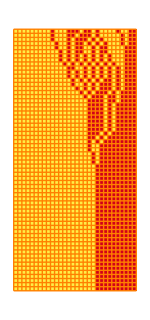
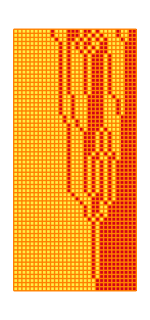
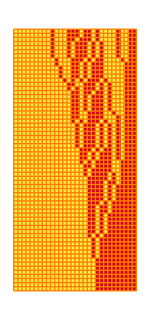
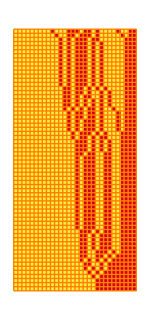

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BlockRandom[SeedRandom[235234];With[{i=RandomInteger[1,30]},Table[ArrayPlot[NestList[First[Sort[{Flatten[MapAt[Sort,Partition[#,2],Union[List/@RandomInteger[{1,Length[#]/2},20]]]],RotateRight[Flatten[MapAt[Sort,Partition[RotateLeft[#],2],Union[List/@RandomInteger[{1,Length[#]/2},20]]]]]}]]&,i,63],ImageSize->{150,Automatic},ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh->True,MeshStyle->Orange],4]]]
```

And the notable feature is that even though the specific evolution in each case is different, the final result is always the same---in this case just corresponding to having all Hue[0.15, 0.72, 1] sorted before Hue[0.98, 1, 0.8200000000000001]. 
It doesn’t work this way for all rules, but for this rule, regardless of the intermediate states that are produced, there is always eventual consistency in the final result.

As it turns out, this kind of phenomenon is crucial in our Physics Project. And indeed the generalization that we call “causal invariance” is what leads, for example, to relativistic invariance. But from the formalism of the Physics Project we also get a general approach to asynchronous evolution: trace all possible “update histories” using a multiway graph. 
Here is the multiway graph for the simple sorting rule above:

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[ToExpression[#2]],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
ResourceFunction["MultiwaySystem"][{{1, 0}->{0, 1}},{{1,0,1,1,0,0,1}},8,"StatesGraph", "StateRenderingFunction" -> getStateRenderingFunction[], VertexSize -> 1.75, PerformanceGoal-> "Quality"]
```

-Graphics-

As expected, all possible update histories eventually converge to the same final state.

So what about the majority rule cellular automaton?  It doesn’t always show eventual consistency, as this example shows:

```mathematica
randomOrderCAFunc[ruleRadius_, ruleNumber_, init_, eventCount_, func_] :=
  func[evaluateSingleEvent[ruleRadius, ruleNumber, #] &, init, eventCount];
```

```mathematica
RandomOrderCA[args___] := randomOrderCAFunc[args, Nest];
```

```mathematica
RandomOrderCAList[args___] := randomOrderCAFunc[args, NestList];
```

```mathematica
findLastEvent[eventNumber_, position_, eventsIndex_] := Module[{},
  Max[Select[Lookup[eventsIndex, position, {-Infinity}], # < eventNumber &]]
];
```

```mathematica
getCausalLinks[eventNumber_, position_, eventsIndex_, size_, ruleRadius_] := Module[{},
  DeleteCases[
    findLastEvent[eventNumber, #, eventsIndex] -> eventNumber & /@
      Mod[Range[position - ruleRadius, position + ruleRadius], size, 1],
    -Infinity -> _]
];
```

```mathematica
RandomOrderCACausalGraph[ruleRadius_, ruleNumber_, init_, eventCount_, opts___] := Module[{eventsIndex, eventPositions},
  eventsIndex = KeySort @ Map[
    Last,
    GroupBy[
      Thread[
        (eventPositions = Reap[RandomOrderCA[ruleRadius, ruleNumber, init, eventCount]][[2, 1]]) ->
          Range[eventCount]],
      First],
    {2}];
  Graph[
    Range[eventCount],
    Catenate[getCausalLinks[#, eventPositions[[#]], eventsIndex, Length[init], ruleRadius] & /@ Range[eventCount]],
    EdgeStyle -> ResourceFunction["WolframPhysicsProjectStyleData"]["CausalGraph", "EdgeStyle"],
    VertexStyle -> ResourceFunction["WolframPhysicsProjectStyleData"]["CausalGraph", "VertexStyle"],
    opts]
]
```

```mathematica
randomInit[size_, onesFraction_] := RandomChoice[{1 - onesFraction, onesFraction} -> {0, 1}, size];
```

```mathematica
evaluateSingleEvent[ruleRadius_, ruleNumber_, init_] :=
  evaluateEventAtPlace[ruleRadius, ruleNumber, init, Sow[RandomInteger[{1, Length[init]}]]];
```

```mathematica
evaluateEventAtPlace[ruleRadius_, ruleNumber_, init_, center_] := Module[{input, newCenterValue},
  input = cyclicTake[init, Range[center - ruleRadius, center + ruleRadius]];
  newCenterValue = CellularAutomaton[{ruleNumber, 2, ruleRadius}, input][[ruleRadius + 1]];
  ReplacePart[init, center -> newCenterValue]
];
```

```mathematica
cyclicTake[list_, indices_] := cyclicPart[list, #] & /@ indices;
```

```mathematica
cyclicPart[list_, index_] := list[[Mod[index, Length[list], 1]]];
```

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[List@@#2],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
SeedRandom[643767+5];SimpleGraph[NestGraph[Table[state@@evaluateEventAtPlace[1, 232, List@@#,c],{c,1,Length[#]}]&,state@@randomInit[9,0.7],20, VertexShapeFunction->getStateRenderingFunction[],  PerformanceGoal->"Quality", VertexSize -> 1,ResourceFunction["WolframPhysicsProjectStyleData"]["StatesGraph", "Options"]]]
```

-Graphics-

So this means that in general it matters in what order asynchronous updates are done, or, in effect, what “path of history” is taken.  But to get a sense of typical behavior, we can consider random sequences of updates.  Here’s an example of what one gets, doing one update per step:

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

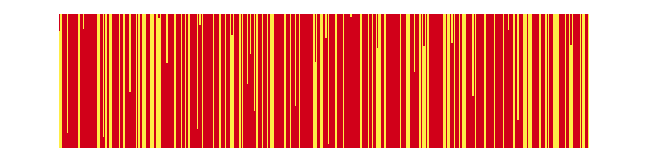

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{232,2,1},RandomChoice[{.7,.3}->{1,0},400],{100,1}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

And here’s the corresponding result if we do 20 updates per step:

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

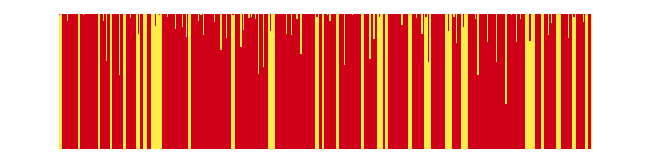

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{232,2,1},RandomChoice[{.7,.3}->{1,0},400],{100,20}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

We might have thought that asynchronous updating would add enough randomness to “break ties” and prevent things getting stuck.  But in fact it’s not hard to see that the results are in this case in the end no different from synchronous updating.

What about for something like the GKL rule?  Here are asynchronous results for it, now with 50 updates per step (with initially 60% Hue[0.98, 1, 0.8200000000000001]):

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

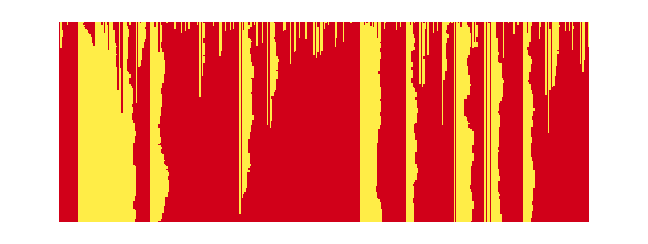

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{339789091192587366278221041213531750560,2,3},RandomChoice[{.6,.4}->{1,0},400],{150,50}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

And unlike what we saw above for synchronous updating when we added noise, the change to asynchronous updating seems to completely destroy “majority consensus” for this rule.  Note that using more updatings per step does not improve the result (which should in the end be Hue[0.98, 1, 0.8200000000000001] not Hue[0.15, 0.72, 1]):

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

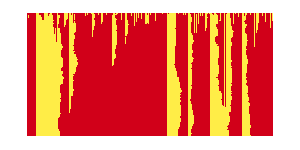
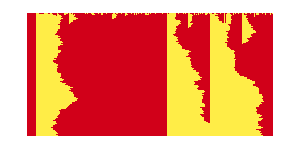
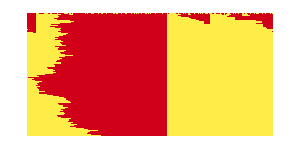
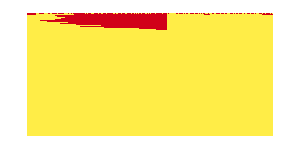
-Graphics-100 | -Graphics-1000
-Graphics-10000 | -Graphics-100000

```mathematica
Grid[Partition[Labeled[BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{339789091192587366278221041213531750560,2,3},RandomChoice[{.6,.4}->{1,0},400],{150,#}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None, ImageSize -> {300, 150}]],Style[#,11], Spacings -> {0,-0.5}]&/@{100,1000,10000,10^5}, 2],Spacings ->{0, 0}]
```

So what happens if we search for rules that achieve consensus asynchronously?  In the nearest-neighbor case, the simple majority rule does best, although it’s basically no good.

Here are results for a few rules found by searching a million range-2 rules:

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

```mathematica
GraphicsGrid[ParallelTable[BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{#,2,2},RandomChoice[{p,1-p}->{1,0},300],{200,400}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->None]],{p,.3,.7,.1}]&/@{4272826020,4242057736,4265795970,3663321792,3953790018,4020250803}]
```

-Graphics-

```mathematica
GraphicsRow[MapIndexed[Labeled[GraphicsColumn[#, ImageSize->130, Spacings -> {0, 2}], Style[Text[StringJoin[ToString[10*(First[#2]+2)], "%"]], 11], Spacings -> {0,-0.3}]&,Transpose[ParallelTable[BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{#,2,2},RandomChoice[{p,1-p}->{1,0},300],{200,400}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->None,ImageSize->125]],{p,.3,.7,.1}]&/@{4272826020,4242057736,4265795970,3663321792,3953790018,4020250803}]],ImageSize->690,Spacings->{0,0}]
```

-Graphics-